# Investment Strategies: Functional Weighted Choice Method

Nam Tran-Hoang

2019-07-09

Disclaimer: ​This computational notebook is not to be sold or exchanged for either monetary or non-monetary gains in anyway. The notebook is not to be modified without prior written consent from the author. ​The calculation only serves as an additional reference for equity investors and investment advisors. Any liability, including any liability for negligence, for any loss or damage arising from reliance on this computational notebook, is expressly excluded.

## I. Abstract

A quantitative model was derived to analyze common collections of investment tactics. The model was designed with flexibility: it can choose and weight the stocks into a portfolio of any size, based on any analytic expression of the stocks’ financial characteristics. Using the model, several common investment strategies were investigated: chosen and weighted by price; chosen by price, equally weighted; chosen by volume, weighted by market capitalization. Consistent with the Capital Asset Pricing Model, the model shows that a well-diversified portfolio exhibits less volatility and less return. The model also indicate that the frequency of adjustment does not exert a strong effect on the strategy’s performance.

## II. Introduction

Equity investing remains a significant vehicle to preserve and generate wealth. Owing to the advances in technology and computational instruments, as well as the readily available financial data, strategical equity investing has become more technically accessible. Yet, apart from large financial institutions (such as hedge-funds and investment banks), the analyzing tools for investment strategies are not readily available to most individual investors – and even when the tools are available, the analysis are often basic and limited. Hence, a mathematically robust, versatile tool for investment strategy would enable more people to participate in investing, to make better-informed choice, which may narrows the standard of living gap between different social classes.

Here, a computational model was derived and freely distributed to help quantifying the most common collection of investment strategies: the model aims to quantify the portfolio’s performance, in which stocks are chosen and weighted based on certain criteria. The model consists of two distinct parts: the gathering of historical data/financial information, and the construction of the portfolios – back-testing on historical data for theoretical performance (taxes, transactional fees, and other necessary costs are not included in the tests).

## III. Data Gathering

```mathematica
ClearAll["Global`*"];
SetDirectory[NotebookDirectory[]];
```

First, a collection of stocks is specified: this collection will serve as the “set of all stocks”, from which the portfolios will be constructed. For the purpose of constructing and testing a computational model, the collection is chosen to be SP500: all the stocks that are listed on the Standard and Poor 500 Index (^SPX)

```mathematica
listStock=EntityList[EntityClass["Financial","SP500"]];
DumpSave["listStock.MX",listStock];
```

This specified “set of all stocks” SP500 is then associated with multiple other financial properties: price, option2, option3, option4, option5, option6. Price is always included, since stock price is necessary to quantify an investment strategy’s performance. The other options are chosen from the following list, so that they result in timeseries (measurements over time) of the properties (as currently supported by Wolfram Mathematica kernel, 2019-07-10): {“Change”, “Close”, “CumulativeFractionalChange”, “Dividend”, “DividendPerShare”, “Last”, “MarketCap”, “Open”, “Price”, “RawVolume”, “Return”, “Volume”}. If an option is not used, that option must be specified as “None”.

The financial properties for the “set of all stocks” are collected with one call of FinanciaData[], in order to minimize the downloading time. Yet, because of the sheer size of the timeseries: all daily data points of several properties of all stocks since the stocks’ inception, the financial properties may take as much as two hours to be procured (the Boolean variable run is used to prevent inadvertently overwriting the obtained data file - it needs to be changed to True in order to execute the codes in this section).

```mathematica
option2="MarketCap";
option3="Volume";
option4="Close";
option5="Open";
option6="None";
listOptions=DeleteCases[{option2, option3, option4, option5, option6},"None"];
DumpSave["listOptions.MX",listOptions];

run=False;
If[run==True,listStockPropRaw=FinancialData[listStock,Prepend[listOptions,"Price"],All]];
```

The portfolios will be compared against a benchmark to assess their performance. This benchmark is chosen to be the Standard and Poor 500 Index (^SPX): the data is stored in sp500All variable.

```mathematica
sp500All=FinancialData["^SPX",All];
DumpSave["sp500All.MX",sp500All];
```

Once all the financial properties are (finally) obtained, the timeseries are changed into interpolation order of 0, which means missing/interval measurements will be identical to its immediately previous measurement, effectively describing a step function (instead of interpolating the interval measurement from both its immediate previous data point and its next data point - i.e. using future data to make a present decision). This step is crucial for back-testing, especially with quarterly (every three months) financial data such as dividend, total asset, total liability, EBITDA (earnings before interest, tax, depreciation and amortization), etc.

(At the moment, Wolfram Research has plan to incorporate EntityValue[] of entity “Company” into the FinancialData[] function, so that by querying a stock, the associated company’s financial and accounting information can be obtained.)

```mathematica
If[run==True,
listStockProp=Replace[listStockPropRaw,List["Interpolation",Rule[InterpolationOrder,1]]->List["Interpolation",Rule[InterpolationOrder,0]],{5}];
DumpSave["listStockProp.MX",listStockProp];
]
```

The SP500 stocks’s name and financial properties are combined into one variable: masterThread, with its definition saved into “masterThreadGeneral.MX”. The variable masterThread is ascertained with its length and an excerpt of its contents.

```mathematica
If[run==True,
CompoundExpression[
masterThreadNotIndexed=
DeleteMissing[
Transpose[Prepend[Transpose[listStockProp],listStock]],
1,3];

masterThread=Transpose[Prepend[Transpose[masterThreadNotIndexed],Range[Length[masterThreadNotIndexed]]]];
DumpSave["masterThreadGeneral.MX",masterThread];

masterThread//Length
RandomSample[masterThread,5]//TableForm//Print
]]
```

For the sole purpose of constructing the computational model, a smaller set of 64 randomly selected stocks from SP500 are obtained (since making a portfolio by sorting the whole 505 stocks in the SP500 set would take a bit longer - which is unnecessary at this stage).

```mathematica
If[run==True,
CompoundExpression[
ClearAll[masterThread];
masterThreadNotIndexedSample=RandomSample[
DeleteMissing[
Transpose[Prepend[Transpose[listStockProp],listStock]],
1,3],64];

masterThread=Transpose[Prepend[Transpose[masterThreadNotIndexedSample],Range[Length[masterThreadNotIndexedSample]]]];
DumpSave["masterThreadSample64.MX",masterThread];

masterThread//Length
RandomSample[masterThread,5]//TableForm//Print
]]
```

## IV. Constructing the computational model

First, the previously constructed listOptions, sp500All, and the masterThread variables are reloaded into a clean Mathematica kernel.

```mathematica
ClearAll["Global`*"];
SetDirectory[NotebookDirectory[]];
Off[InterpolatingFunction::dmval];

Get["listOptions.MX"];
Get["sp500All.MX"];
Get["masterThreadSample64.MX"];
```

The inputs for the computational model are specified:
	timePeriod denotes the portfolio’s frequency of adjustment in days: timePeriod = n means that the portfolio is updated/adjusted every n days.
	sizePortfolio denotes the portfolio’s size – the pre-specified number of stocks the portfolio contains. Obviously, the portfolio size much be smaller than the number of stocks in masterThread.
	
	beginDate denotes the first date of the investigated time window.
	endDate denotes the last date of the investigated time window.
	
	funcSort[] determines how the stocks in masterThread (the “set of all stocks”) at one specific instant of time are sorted for selection, from largest to smallest. Function funcSort accepts any analytic expression of x1, x2, x3, x4, x5,..., corresponding to the financial properties ”Price”, option2, option3, option4, option5,...
	
	optionTake, which is linked to funcTake[] on the following paragraph, specified how the stocks are collected into a portfolio from the sorted  masterThread (using funcSort). Variable optionTake is designed to accept only three designation: “high”, meaning the largest stocks are taken (with respect to their metrics obtained from funcSort); “low”, meaning the smallest stocks are taken; and mid”, meaning the middle stocks are taken.
	
	funcWeight[] determines how the selected stocks in the portfolio are weighted for investment. Function funcWeight accepts any analytic expression of x1, x2, x3, x4, x5,..., corresponding to the financial properties “Price”, option2, option3, option4, option5,... To use funcWeight, optionEqualWeight must be False.
	
	optionEqualWeight denotes whether to use funcWeight[], or to assign equal weight to all selected stocks in the portfolio. Variable optionEqualWeight accepts only Boolean values True or False.
	
	portValue[beginDate] specifies the initial amount of money invested in the portfolio.

```mathematica
timePeriod=16;
sizePortfolio=10;

beginDate=DateObject["2012-06-01"];
endDate=DateObject["2019-06-01"];

funcSort[x1_,x2_,x3_,x4_,x5_]:=x2+x3;

optionTake="low"; (*high mid low*)

funcWeight[x1_,x2_,x3_,x4_,x5_]:=x5-x4+x1;
optionEqualWeight=False;

portValue[beginDate]=Quantity[1,"USDollars"];
```

Function funcTake[], mentioned earlier with variable optionTake, is defined to execute the input given to optionTake.
Variable sp500Ratio stores the relative value of the Standard and Poor 500 Index (^SPX) since the first date of the investigated time window – of which the portfolio performance is compared against.

```mathematica
funcTake[sortedListVar_,sizePortfolioVar_]:=Which[
optionTake=="high",Take[sortedListVar,sizePortfolioVar],
optionTake=="mid",Take[sortedListVar,{Floor[(Length[sortedListVar]-sizePortfolioVar)/2],Floor[(Length[sortedListVar]+sizePortfolioVar)/2]-1}],
optionTake=="low",Take[sortedListVar,-sizePortfolioVar]
];

sp500=TimeSeriesWindow[sp500All,{beginDate,endDate},IncludeWindowTimes->True,ResamplingMethod->{"Interpolation",InterpolationOrder->0}];
sp500Ratio=sp500/QuantityMagnitude[sp500[beginDate]];
```

The function callFuncBody[] constitutes the essence of the model: it determines the portfolio’s value at each instant of adjustment. Initially, the function distributes the starting investment amount to the chosen list of stocks (sorted by funcSort, chosen by optionTake/funcTake, and weighted by funcWeight), from which it registers the number of shares of the chosen stocks. At the next date of adjustment, the function uses the previous number of shares and new stock prices to compute the new portfolio value – which is then used to derive the new number of shares, etc. The function repeats the process until it spans over the whole pre-specified time window. The portfolio value is capped at 100 times the original amount of investment.

The function callFunc[] imposes necessary conditions on callFuncBody[]: the model will only evaluates with proper inputs. Additionally, the function callFunc[] appends further processing steps into the model.

```mathematica
(*callFuncBody[]*)
callFuncBody[]:=Module[{threadPrevious={},indexPrevious={},threadAtTime,newPriceList,threadAtTimeAppend,sortedList,sortList,weightList,listChosen,weight,t,tprevious},
listDate={};
TimeConstrained[For[t=beginDate,t≤ endDate,t=DatePlus[t,timePeriod],
threadAtTime=MapAt[#[t]&,masterThread,{All,{3,4,5,6,7}}];

If[And[FreeQ[QuantityMagnitude[threadAtTime],_Missing,2],threadAtTime≠threadPrevious],
CompoundExpression[

If[indexPrevious≠{},
newPriceList=Select[threadAtTime,MemberQ[indexPrevious,#[[1]]]&][[All,3]];
portValue[t]=Min[100portValue[beginDate],Dot[newPriceList,listShareNumber[tPrevious]]];
];

sortList=funcSort[x1,x2,x3,x4,x5]/.{
x1->QuantityMagnitude[threadAtTime[[All,3]]],
x2->QuantityMagnitude[threadAtTime[[All,4]]],
x3->QuantityMagnitude[threadAtTime[[All,5]]],
x4->QuantityMagnitude[threadAtTime[[All,6]]],
x5->QuantityMagnitude[threadAtTime[[All,7]]]};

weightList=If[optionEqualWeight==False,
funcWeight[x1,x2,x3,x4,x5]/.{
x1->QuantityMagnitude[threadAtTime[[All,3]]],
x2->QuantityMagnitude[threadAtTime[[All,4]]],
x3->QuantityMagnitude[threadAtTime[[All,5]]],
x4->QuantityMagnitude[threadAtTime[[All,6]]],
x5->QuantityMagnitude[threadAtTime[[All,7]]]
},
ConstantArray[1/Length[masterThread],Length[masterThread]]
];

threadAtTimeAppend=Transpose[Join[Transpose[threadAtTime],{sortList},{weightList}]];

sortedList=Sort[threadAtTimeAppend,#1[[-2]]>#2[[-2]]&];

listChosen=funcTake[sortedList,sizePortfolio];
weight=If[And[optionEqualWeight==False,0<QuantityMagnitude[Min[listChosen[[All,-1]]]],QuantityMagnitude[Max[listChosen[[All,-1]]]]<∞],
listChosen[[All,-1]]/Total[listChosen[[All,-1]]],
ConstantArray[1/sizePortfolio,sizePortfolio]
];
listShareNumber[t]=weight*portValue[t]/listChosen[[All,3]];
portAtTime[t]=Thread[{listChosen[[All,1]],listChosen[[All,2]],listChosen[[All,3]],listShareNumber[t]}];

Do[
shareNo[listChosen[[i,1]],t]=listShareNumber[t][[i]],
{i,1,Length[listChosen]}
];

Do[
shareNo[n,t]=0,
{n,Complement[Range[Length[masterThread]],listChosen[[All,1]]]}
];

AppendTo[listDate,t];
threadPrevious=threadAtTime;
tPrevious=t;
indexPrevious=listChosen[[All,1]];

](*CompoundExpression*)](*If*)
](*For*),
10*60,Print["Time Out!"](*TimeConstrained*)];
](*Module*);

(*callFunc[]*)
callFunc[]:=If[
And[
Length[masterThread]>sizePortfolio,
beginDate≤ endDate,
IntegerQ[timePeriod],
BooleanQ[optionEqualWeight],
MemberQ[{"high","mid","low"},optionTake]
](*And*),

CompoundExpression[
callFuncBody[];

Do[
shareNumberTimeSeries[n]=TimeSeries[Table[shareNo[n,t],{t,listDate}],{listDate}],
{n,1,Length[masterThread]}
](*Do*);

portValueTimeSeries=TimeSeries[Table[portValue[t],{t,listDate}],{listDate},ResamplingMethod->{"Interpolation",InterpolationOrder->0}];
finalList=Transpose[Append[Transpose[masterThread],Table[shareNumberTimeSeries[n],{n,1,Length[masterThread]}]]];

](*CompoundExpression*),

Print["Error: problematic input(s)! Model will not run."]
](*If*);
```

Function callFunc[] defines several global variables:
	listDate: the list of all the dates at which the portfolio was adjusted.
	portAtTime[t]: the component of the portfolio at an instance of time t. The instance of time t must be an element of the list of all date listDate.
	shareNumberTimeSeries[n]: the timeseries of the share number in portfolio of the nth stock in masterThread (1 ≤ n ≤ Length[masterThread])
	portValueTimeSeries: the timeseries of portfolio value.
	finalList: the list of all stocks and their properties, with their share number appended.

```mathematica
callFunc[];

Hold[
Take[listDate,6]//TableForm//Print;
Table[{t,portAtTime[t]},{t,listDate}]//TableForm//Print;
Table[{n,shareNumberTimeSeries[n]},{n,1,6}]//TableForm//Print;
portValueTimeSeries//Print;
Take[finalList,5]//TableForm//Print;
];
```

Here is an example of the finalList, with appropriate annotation.

```mathematica
finalListHeadings=Style[Framed[#],16]&/@Flatten[{"No.","Name","Price",listOptions,"No. of shares in portfolio"}];
finalListwithHeadings=Insert[finalList,finalListHeadings,{{1},{-1}}];

Rasterize[Take[finalListwithHeadings,6]//TableForm,RasterSize->2048,ImageSize->2048]
```

-Graphics-

Here is an example of the portAtTime, with appropriate annotation.

```mathematica
portfolioAtTimeHeadings=Style[Framed[#],16]&/@{"No.","Name","Price","No. of shares in portfolio"};
portfolioAtTime=Insert[portAtTime[RandomChoice[listDate]],portfolioAtTimeHeadings,{{1},{-1}}];

Take[portfolioAtTime,12]//TableForm//Print
```

No. | Name | Price | No. of shares in portfolio
28 | Evergy Inc | 57.01 $ | 0.00560657
27 | Broadridge | 65.16 $ | 0.00562598
29 | Wabtec | 85.63 $ | 0.00566553
48 | Cadence | 26.40 $ | 0.00575894
42 | Fluor | 51.34 $ | 0.00564381
63 | People's United | 18.29 $ | 0.00564339
45 | Abiomed | 113.41 $ | 0.0056422
55 | Lamb Weston Holdings Inc | 32.68 $ | 0.00554408
49 | Pentair | 44.51 $ | 0.00548905
19 | NRG Energy | 11.21 $ | 0.0056674
No. | Name | Price | No. of shares in portfolio

Function callPlot[] is defined to expeditiously visualize the portfolio performance in comparison with the Standard and Poor 500 Index.
Function callExport[] will save the graph as a .PNG file, at the notebook’s directory.

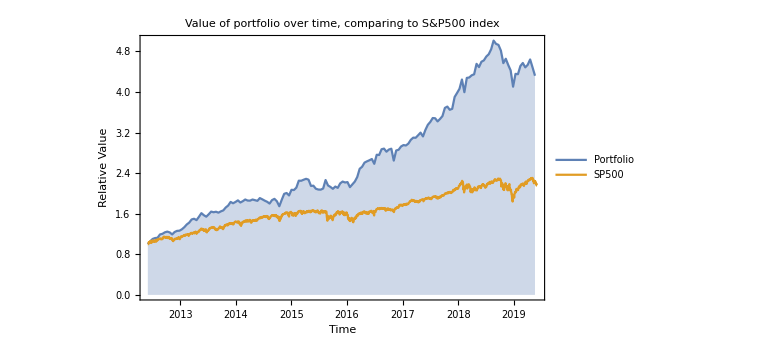

```mathematica
callPlot[]:=Module[{},
frameLabel=Style[Framed[#],12]&/@{"Time","Relative Value"};
plotLabel=Style[Framed["Value of portfolio over time, comparing to S&P500 index"],16];
max=Max[Min[QuantityMagnitude[Max[portValueTimeSeries]],6],Max[sp500Ratio]];
min=Min[Max[QuantityMagnitude[Min[portValueTimeSeries]],-1],Min[sp500Ratio]];
plot=DateListPlot[{portValueTimeSeries,sp500Ratio},FrameLabel->frameLabel,PlotLabel->plotLabel,PlotRange->{Automatic,{0,max}},PlotStyle->{Thick,Thick},Filling->{1->Axis,2->{{1},{None,Directive[Opacity[0.3],ColorData[97,"ColorList"][[2]]]}}},FillingStyle->Opacity[0.3],PlotLegends->{"Portfolio","SP500"},ImageSize->Large]
];

callExport[]:=Export[
StringJoin["plot01",
StringTake[ToString[optionTake],2],
StringPadLeft[ToString[timePeriod],2,"0"],
StringPadLeft[ToString[sizePortfolio],2,"0"],
".png"
]
,plot];

plotlo1610=callPlot[]
callExport[];
```

## V. Analysis of investment strategies

### 1) An arbitrary strategy

An arbitrary, simple strategy was chosen to illustrate some general characteristics of investment: sorted by the sum of Volume and Market Capitalization, and weighted by Price + Open – Close.

```mathematica
funcSort[x1_,x2_,x3_,x4_,x5_]:=x2+x3;
funcWeight[x1_,x2_,x3_,x4_,x5_]:=x5-x4+x1;
optionEqualWeight=False;

reEvaluateFunc[optionTakeVar_,timePeriodVar_,sizePortfolioVar_,export_]:=Module[{o=optionTakeVar,t=timePeriodVar,s=sizePortfolioVar,ex=export},
timePeriod=t;
sizePortfolio=s;
optionTake=o;

callFunc[];
If[ex==True,callExport[]];
callPlot[]
]

plothi1610=reEvaluateFunc["high",16,10,True];
plothi6410=reEvaluateFunc["high",64,10,True];
plothi1630=reEvaluateFunc["high",16,30,True];

plotlo1610=reEvaluateFunc["low",16,10,True];
plotlo6410=reEvaluateFunc["low",64,10,True];
plotlo1630=reEvaluateFunc["low",16,30,True];
```

For this arbitrary investment analysis, the frequency of adjustment does not exert a strong effect on the strategy’s performance, as evidenced in the similar shape and scale of the plots on the first and second columns of each row.
Independent of how the stocks are choosen (largest – high and smallest – low), a bigger portfolio exhibits less deviation from the parental Standard and Poor 500 Index, as indicated through the graphs of the second and third columns.
Regarding this particular strategy over the chosen time period, choosing the smallest stocks seems to be twice as profitable as passive investing in SP500 Index, yielding a 4.32 times profit, corresponding to a yearly return of 23.2%.

```mathematica
k=32;
line1=Style[Framed["Largest\nStocks"],k];
line2=Style[Framed["Smallest\nStocks"],k];
col1=Style[Framed["Higher Frequency"],k];
col2=Style[Framed["Base Case"],k];
col3=Style[Framed["Bigger Portfolio"],k];

plotList1={{"",col1,col2,col3},{line1,plothi6410,plothi1610,plothi1630},{line2,plotlo6410,plotlo1610,plotlo1630}};
Rasterize[TableForm[plotList1,TableAlignments->Center],ImageSize->Full]
```

-Graphics-

### 2) The sorted and weighted by price strategy

A common strategy involving portfolio of stocks sorted and weighted by price was also investigated.

```mathematica
funcSort[x1_,x2_,x3_,x4_,x5_]:=x1;
funcWeight[x1_,x2_,x3_,x4_,x5_]:=x1;
optionEqualWeight=False;

plot02hi10=reEvaluateFunc["high",16,10,False];
plot02hi30=reEvaluateFunc["high",16,30,False];

plot02lo10=reEvaluateFunc["low",16,10,False];
plot02lo30=reEvaluateFunc["low",16,30,False];
```

```mathematica
k=32;
head=Style[Framed["Sorted and Weighted by Price"],k];
line1=Style[Framed["Largest\nStocks"],k];
line2=Style[Framed["Smallest\nStocks"],k];
col1=Style[Framed["Base Case"],k];
col2=Style[Framed["Bigger Portfolio"],k];

plotList2={{"",col1,col2},{line1,plot02hi10,plot02hi30},{line2,plot02lo10,plot02lo30},{head,SpanFromLeft,SpanFromLeft}};
Rasterize[TableForm[plotList2,TableAlignments->Center],ImageSize->Full]
```

-Graphics-

For this strategy, the smaller stocks also give better return over time.

### 3) The sorted by price, equally weighted strategy

```mathematica
funcSort[x1_,x2_,x3_,x4_,x5_]:=x1;
funcWeight[x1_,x2_,x3_,x4_,x5_]:=x1;
optionEqualWeight=True;

plot03hi10=reEvaluateFunc["high",16,10,False];
plot03hi30=reEvaluateFunc["high",16,30,False];

plot03lo10=reEvaluateFunc["low",16,10,False];
plot03lo30=reEvaluateFunc["low",16,30,False];
```

```mathematica
k=32;
head=Style[Framed["Sorted by Price, Equally Weighted"],k];
line1=Style[Framed["Largest\nStocks"],k];
line2=Style[Framed["Smallest\nStocks"],k];
col1=Style[Framed["Base Case"],k];
col2=Style[Framed["Bigger Portfolio"],k];

plotList2={{"",col1,col2},{line1,plot03hi10,plot03hi30},{line2,plot03lo10,plot03lo30},{head,SpanFromLeft,SpanFromLeft}};
Rasterize[TableForm[plotList2,TableAlignments->Center],ImageSize->Full]
```

-Graphics-

This looks problematic. I am skeptical that the strategy can perform that well against the SP500 benchmark.

### 4) The sorted by volume, weighted by market capitalization strategy

```mathematica
funcSort[x1_,x2_,x3_,x4_,x5_]:=x3;
funcWeight[x1_,x2_,x3_,x4_,x5_]:=x2;
optionEqualWeight=False;

plot03hi10=reEvaluateFunc["high",16,10,False];
plot03hi30=reEvaluateFunc["high",16,30,False];

plot03lo10=reEvaluateFunc["low",16,10,False];
plot03lo30=reEvaluateFunc["low",16,30,False];
```

```mathematica
k=32;
head=Style[Framed["Sorted by Volume, Weighted by Market Capitalization"],k];
line1=Style[Framed["Largest\nStocks"],k];
line2=Style[Framed["Smallest\nStocks"],k];
col1=Style[Framed["Base Case"],k];
col2=Style[Framed["Bigger Portfolio"],k];

plotList2={{"",col1,col2},{line1,plot03hi10,plot03hi30},{line2,plot03lo10,plot03lo30},{head,SpanFromLeft,SpanFromLeft}};
Rasterize[TableForm[plotList2,TableAlignments->Center],ImageSize->Full]
```

-Graphics-

This looks problematic also. I do not trust it either. Do not ask me why it is as it is. I may dive into the code again when I have time. Again, use this computation model at your own risk.

## VI. Conclusions

A versatile computation model for portfolio’s performance was derived, which allows investment strategies to be analyzed and quantified. The model showed that the frequency of adjustment did not exert a strong effect on the strategy’s performance, which supports the buy-and-hold tactic. Similarly, the model indicated that a bigger portfolio exhibited less volatility – less deviation from the market benchmark, in agreement with the Capital Asset Pricing Model.
Generally, the model suggests that portfolios of small stocks (with respect to the properties investigated) seem to outperform portfolios of larger stocks.